```mathematica
functions={
Sin[x],
Clip[1-Abs[x]],
ⅇ^(-x^2/2),
Clip[x],
Mod[x,1]
};
```

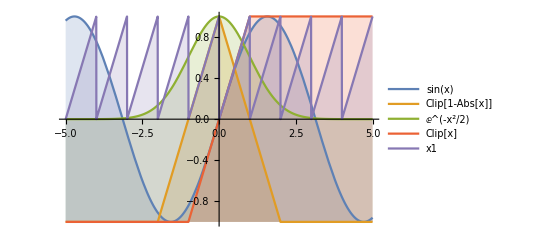

```mathematica
Plot[functions,{x,-5,5},
PlotLegends->"Expressions",
Exclusions->None,
Filling->Bottom]
```

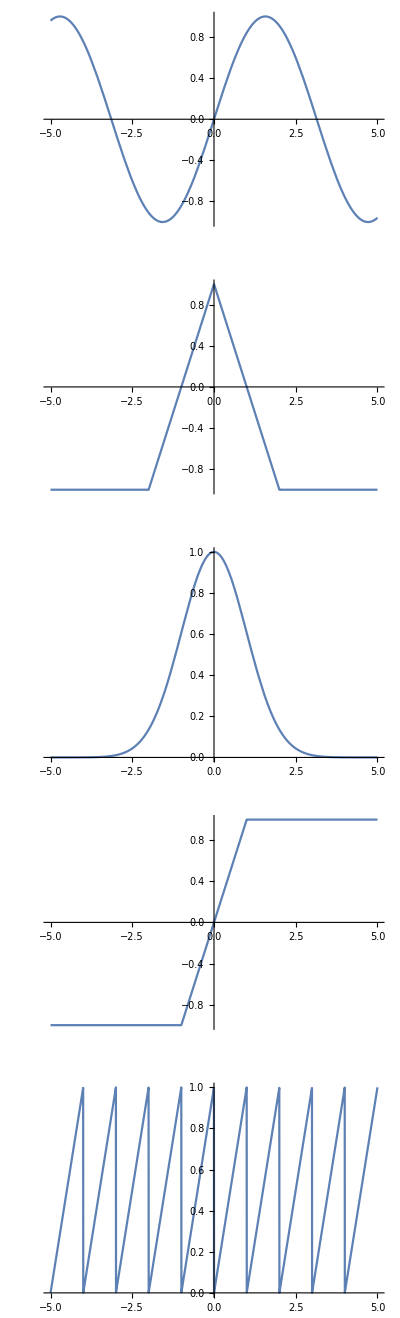

```mathematica
plot=Plot[#,{x,-5,5},Exclusions->None]&/@functions//GraphicsColumn
```

```mathematica
Export["ActivationFunctions.png",plot,ImageResolution->600]
```

ActivationFunctions.png

```mathematica
SystemOpen["ActivationFunctions.emf"]
```

```mathematica
ab[x_]:=Clip[1-Abs[x]];
id[x_]:=Clip[x];
```

```mathematica
f[x_,y_]:=
{
ab[id[x]+ab[id[y]]],
ab[ab[id[y]]],
id[id[y]]
}
```

```mathematica
f[-2,0]
```

{1,0,0}

```mathematica
id[-1]
```

-1

```mathematica
ab[-1]
```

0

```mathematica
col[x_,y_]:=Ordering[f[x,y],-1]//First
```

```mathematica
Table[{col[x,y],f[x,y],{x,y}},{x,-2,2},{y,-2,2}]//MatrixForm
```

((2
{0,1,-1}
{-2,-2}) | (2
{0,1,-1}
{-2,-1}) | (1
{1,0,0}
{-2,0}) | (3
{0,1,1}
{-2,1}) | (3
{0,1,1}
{-2,2})
(2
{0,1,-1}
{-1,-2}) | (2
{0,1,-1}
{-1,-1}) | (1
{1,0,0}
{-1,0}) | (3
{0,1,1}
{-1,1}) | (3
{0,1,1}
{-1,2})
(2
{1,1,-1}
{0,-2}) | (2
{1,1,-1}
{0,-1}) | (3
{0,0,0}
{0,0}) | (3
{1,1,1}
{0,1}) | (3
{1,1,1}
{0,2})
(2
{0,1,-1}
{1,-2}) | (2
{0,1,-1}
{1,-1}) | (3
{-1,0,0}
{1,0}) | (3
{0,1,1}
{1,1}) | (3
{0,1,1}
{1,2})
(2
{0,1,-1}
{2,-2}) | (2
{0,1,-1}
{2,-1}) | (3
{-1,0,0}
{2,0}) | (3
{0,1,1}
{2,1}) | (3
{0,1,1}
{2,2}))